# Fractals and scaling

## Koch Curve

## Drawings

```mathematica
KochCurve[2]
```

Line[{{0.,0.},{0.111111,0.},{0.166667,0.096225},{0.222222,0.},{0.333333,0.},{0.388889,0.096225},{0.333333,0.19245},{0.444444,0.19245},{0.5,0.288675},{0.555556,0.19245},{0.666667,0.19245},{0.611111,0.096225},{0.666667,0.},{0.777778,0.},{0.833333,0.096225},{0.888889,0.},{1.,0.}}]

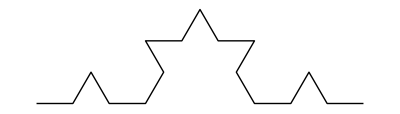

```mathematica
Graphics[KochCurve[2]]
```

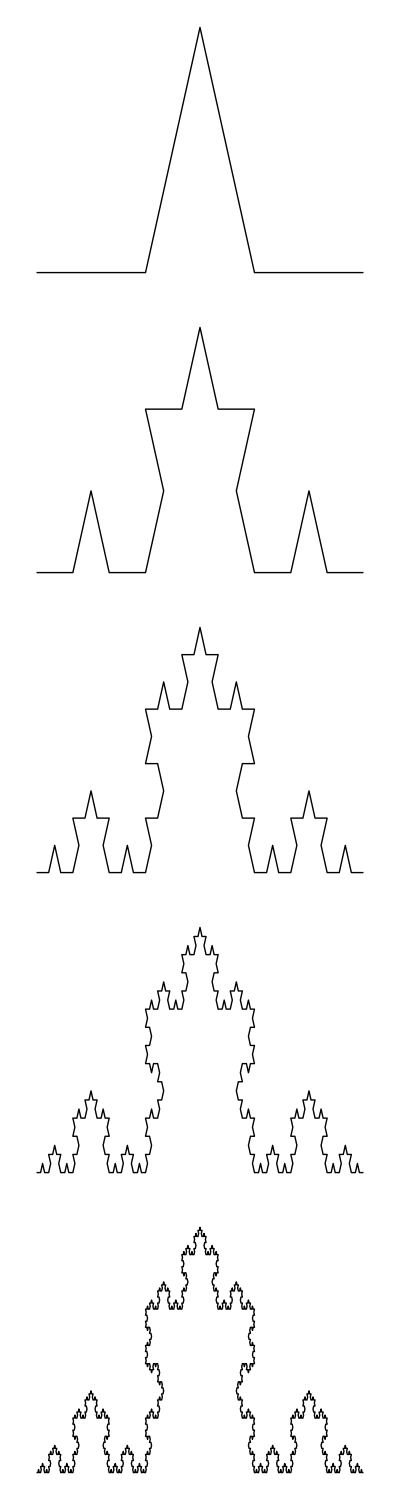

```mathematica
Column[Table[Graphics[KochCurve[n]],{n,1,5}]]
```

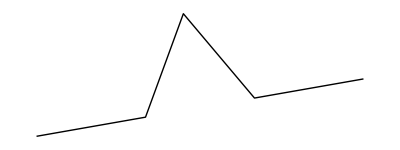
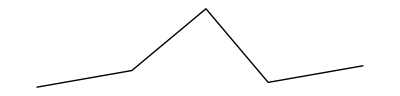
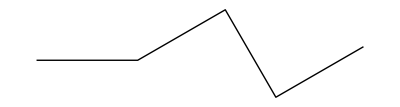

```mathematica
Row[{Graphics[KochCurve[1,{10 °,60 °,-120 °,60 °}]],Graphics[KochCurve[1,{10 °,30 °,-90 °,60 °}]],Graphics[KochCurve[1,{0,30 °,-90 °,90 °}]]}]
```

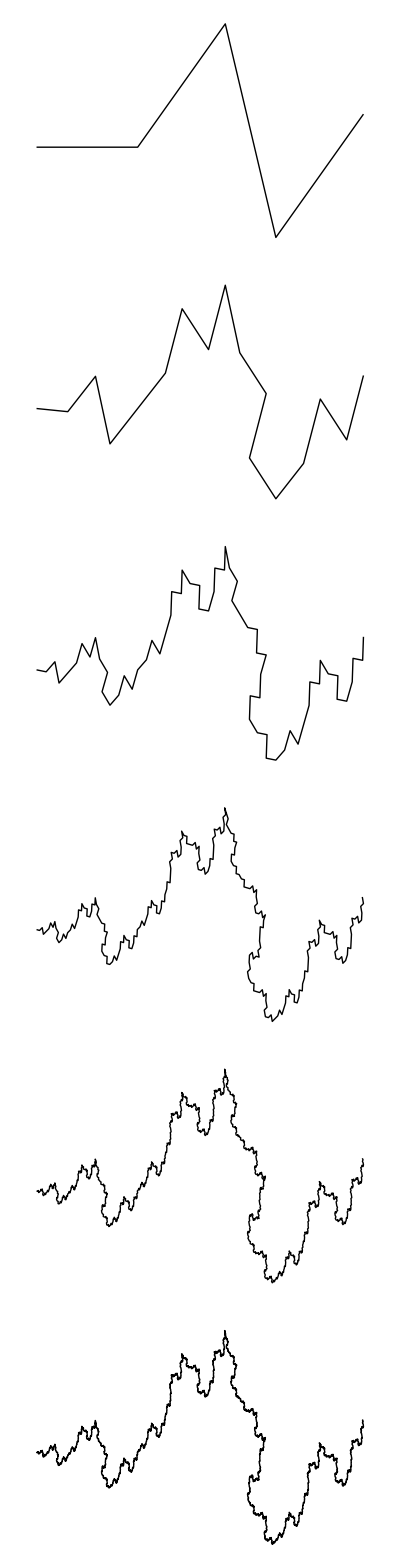

```mathematica
Column[Table[Graphics[KochCurve[n,{0,30 °,-90 °,90 °}]],{n,1,6}]]
```

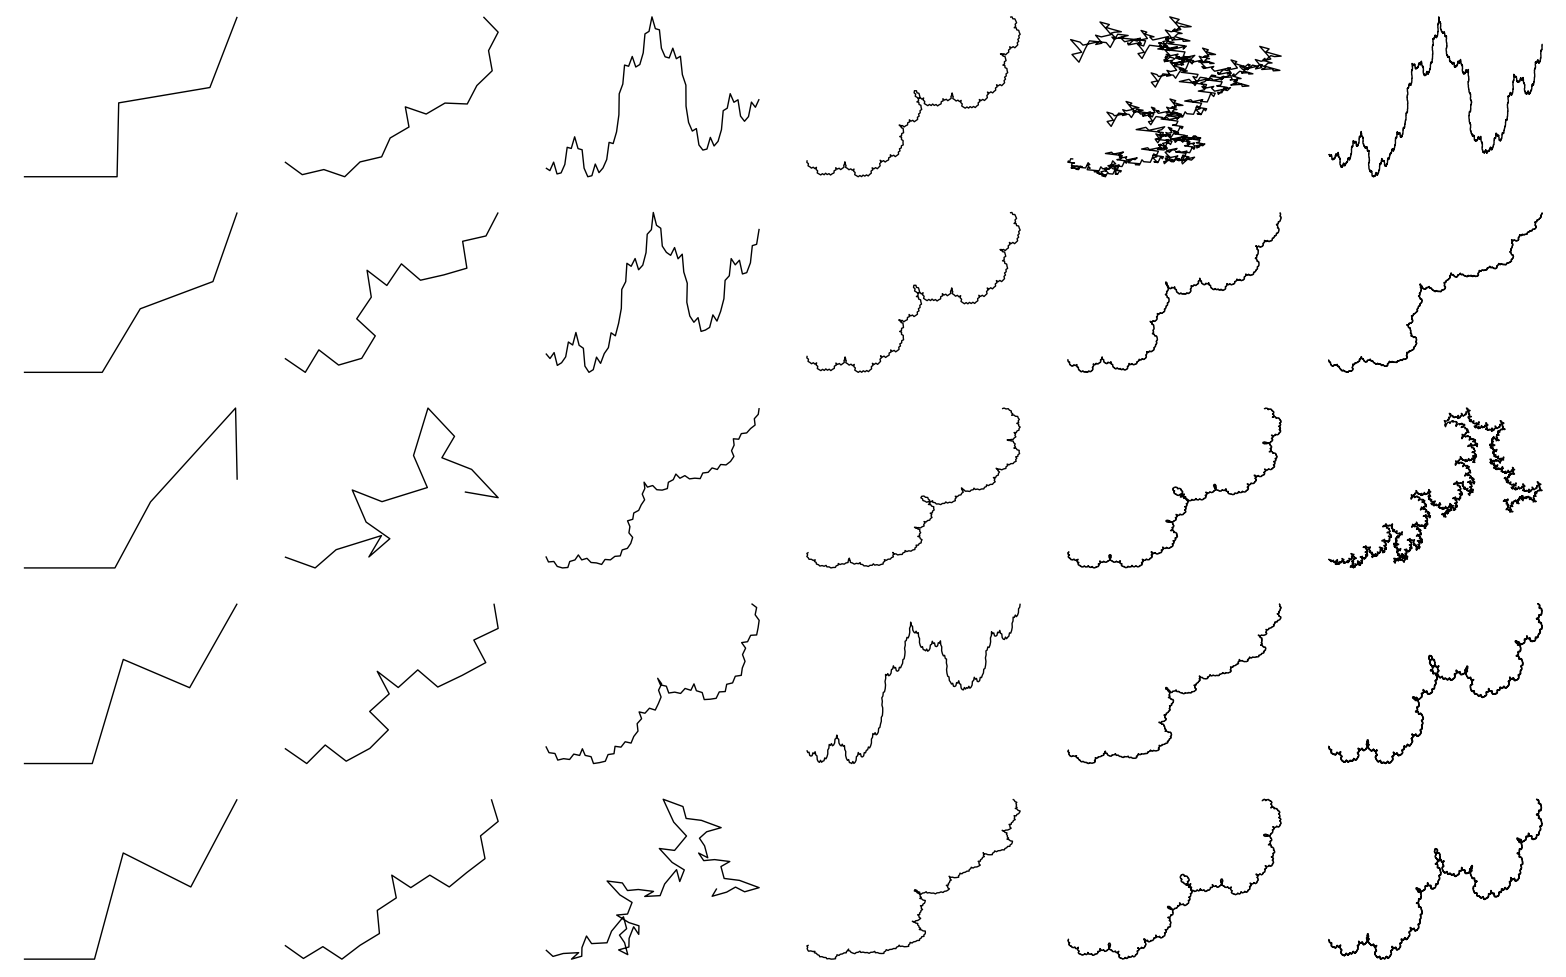

```mathematica
Grid[Table[Table[Graphics[KochCurve[n,{0,RandomInteger[{30,90}] °,-RandomInteger[{30,90}] °,RandomInteger[{30,90}] °}]],{n,1,6}],{i,1,5}]]
```

### TODO: Show the parameters!

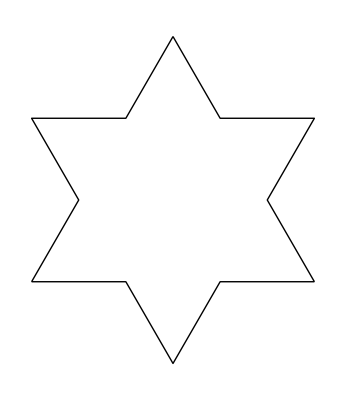
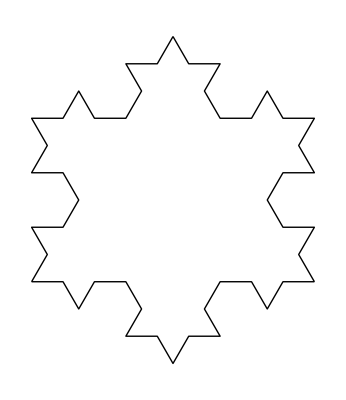
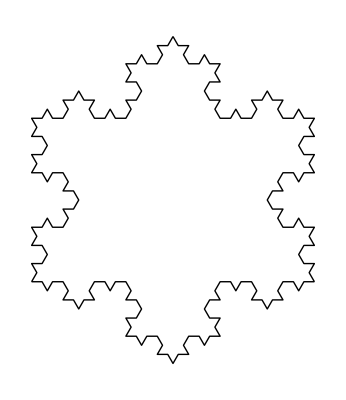
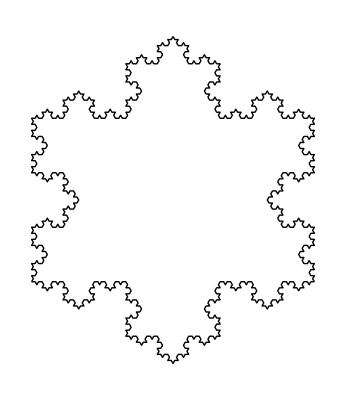

```mathematica
Table[Graphics[GeometricTransformation[KochCurve[i],{RotationTransform[Pi,{1/2,0}],RotationTransform[-Pi/3,{1,0}],RotationTransform[Pi/3,{0,0}]}]],{i,4}]
```

```mathematica
KochCurve[2]
```

Line[{{0.,0.},{0.111111,0.},{0.166667,0.096225},{0.222222,0.},{0.333333,0.},{0.388889,0.096225},{0.333333,0.19245},{0.444444,0.19245},{0.5,0.288675},{0.555556,0.19245},{0.666667,0.19245},{0.611111,0.096225},{0.666667,0.},{0.777778,0.},{0.833333,0.096225},{0.888889,0.},{1.,0.}}]

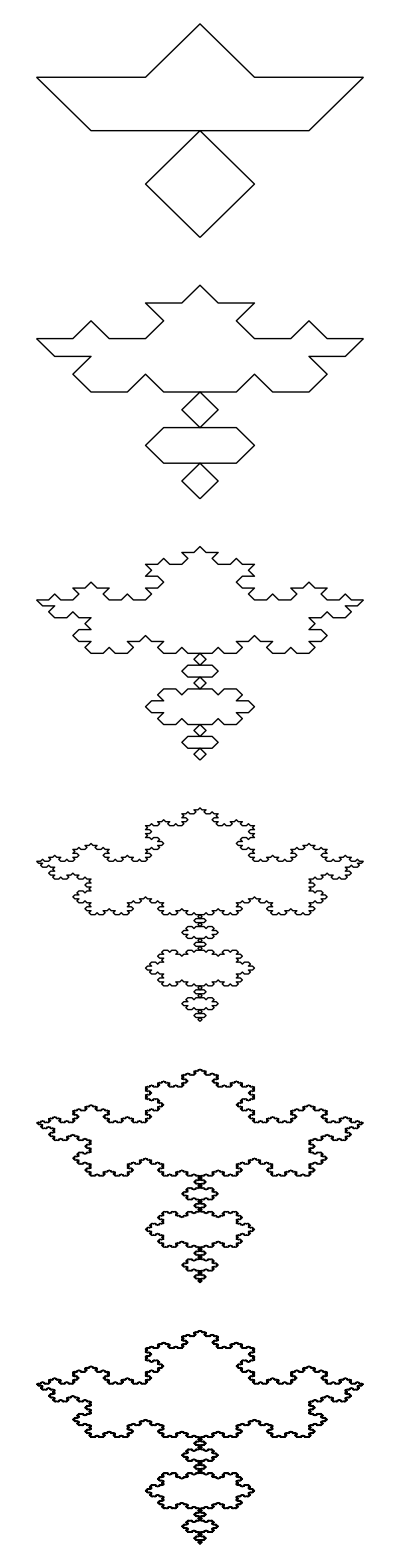

```mathematica
Column[Table[Graphics[GeometricTransformation[KochCurve[n],{RotationTransform[0,{0,0}],RotationTransform[-Pi/3,{0,0}],RotationTransform[Pi/3,{1,0}]}]],{n,1,6}]]
```

### TODO:

## Properties

### TODO: Area/perimeter/ fractal dimension/etc...

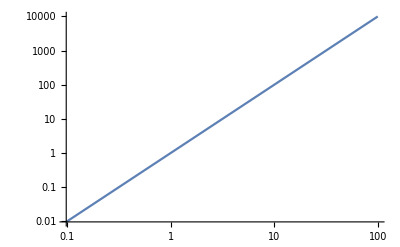

0.788011

```mathematica
LogLogPlot[x^2,{x,0,100}]
```

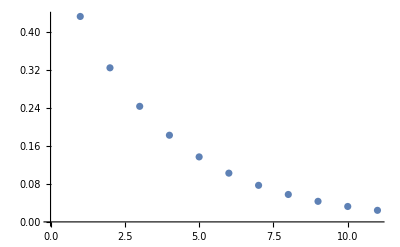

```mathematica
ListPlot[Table[Area[SierpinskiMesh[n]],{n,0,10}]//RootApproximant]
```